```mathematica
link=Install[LinkConnect["36491@192.168.150.128,39955@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θb=0.18,ωb=14.2302,ωe=150,
ωp ={0.039893,0.143882,0.348679,0.597894,0.815419,0.984766,1.11653,1.21888,1.29599,1.34998,1.38201,1.39263,1.38201,1.34998,1.29599,1.21888,1.11653,0.984766,0.815419,0.597894,0.348679,0.143882,0.039893},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd,vr]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe},{ωb,ωe},{θb,θe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
sol=With[{k=4.7,wna=88.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[4.0,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

{2.67588-0.123816 ⅈ,2.68482-0.104287 ⅈ,2.69196-0.0840562 ⅈ,2.69929-0.0618522 ⅈ,2.71005-0.0373607 ⅈ,2.72738-0.0132451 ⅈ,2.75061+0.00654949 ⅈ,2.77715+0.0206693 ⅈ,2.80518+0.0293915 ⅈ,2.83351+0.0330858 ⅈ,2.86111+0.0317274 ⅈ,2.88637+0.0248798 ⅈ,2.90648+0.0126256 ⅈ,2.91861-0.00195083 ⅈ,2.92408-0.0143735 ⅈ}

{2.67588-0.123816 ⅈ,2.68482-0.104287 ⅈ,2.69196-0.0840562 ⅈ,2.69929-0.0618522 ⅈ,2.71005-0.0373607 ⅈ,2.72738-0.0132451 ⅈ,2.75061+0.00654949 ⅈ,2.77715+0.0206693 ⅈ,2.80518+0.0293915 ⅈ,2.83351+0.0330858 ⅈ,2.86111+0.0317274 ⅈ,2.88637+0.0248798 ⅈ,2.90648+0.0126256 ⅈ,2.91861-0.00195083 ⅈ,2.92408-0.0143735 ⅈ,2.92628-0.023611 ⅈ,2.92711-0.0304286 ⅈ,2.92728-0.0355837 ⅈ,2.92709-0.0395883 ⅈ,2.92667-0.0427626 ⅈ,2.92611-0.045325 ⅈ,2.92546-0.0474341 ⅈ,2.92475-0.0492033 ⅈ,2.924-0.0507158 ⅈ,2.92321-0.0520336 ⅈ,2.92241-0.0532035 ⅈ,2.92157-0.0542611 ⅈ,2.92072-0.0552343 ⅈ,2.91984-0.0561417 ⅈ,2.91894-0.0569936 ⅈ,2.91801-0.0577998 ⅈ}

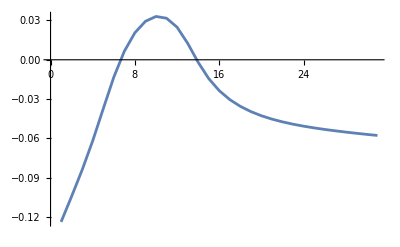

```mathematica
sol1=With[{k=Range[3.2,2.5,-0.05],wna=83Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.0,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[3.25,4.0,0.05],wna=83Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.0,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]]
sol=Join[sol1,sol2[[2,2]]]
ListLinePlot[Im[sol]]
```

```mathematica
Export["89originim-4,3.5-6.0.csv",Im[sol]];

Export["89originre-4,3.5-6.0.csv",Re[sol]];
```